## Interval

### Random Ray

```mathematica
d=Interval[{.1+3.2 I,-.2-.1 I}];
n=300;hf=IFun[Cos,d,n];
hf2=IFun[Exp[-#^2]/.Underflow[]->0&,d,n];
x=MapFromInterval[hf,0.1];
```

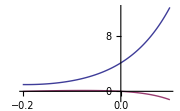

```mathematica
hf
```

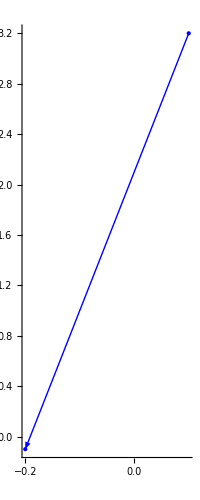

```mathematica
hf//DomainPlot
```

#### addition and mult

```mathematica
(hf+hf2)[x]-(Cos[x]+Exp[-x^2])//Chop
```

0

```mathematica
(hf hf2)[x]-(Cos[x] Exp[-x^2])//Chop
```

0

```mathematica
Sin[hf][x]-Sin[Cos[x]]//Chop
```

0

#### Values Derivatives and Integrals

```mathematica
hf[x]-Cos[x]//Chop
```

0

```mathematica
hf'[x]-Cos'[x]//Chop
```

0

```mathematica
hf''[x]-Cos''[x]//Chop
```

0

```mathematica
(hf//ReduceDimensionIntegrate//Derivative)-hf//Chop//Values//Norm
```

2.36399×10^-10

```mathematica
Integrate[hf][x]-NIntegrate[Cos[MapFromInterval[hf,z]] MapFromIntervalD[hf,z],{z,-1,MapToInterval[hf,x]}]//Chop
```

0

### Adaptive

```mathematica
IFun[Exp,Interval[{0,1}],InterpolationPrecision->10.^(-5)][0.2]-Exp[0.2]
```

-1.72368×10^-6

```mathematica
Chop[IFun[Exp,Line[{0,1}],InterpolationPrecision->10.^(-5)][0.2]-Exp[0.2],10^(-5)]
```

0.0000221751

```mathematica
IFun[Sech,Interval[{0,∞}]][0.4]-Sech[0.4]
```

2.33147×10^-15

## Half Line

### Normal Ray

```mathematica
n=100;hf=IFun[Sech,Interval[{0,∞},Stretch->1],n];
hf2=IFun[Exp[-#^2]&,Interval[{0,∞},Stretch->1],n];
```

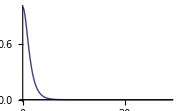

```mathematica
hf
```

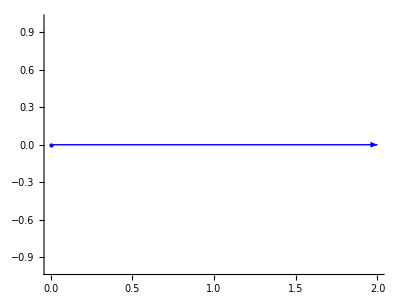

```mathematica
hf//DomainPlot
```

#### addition and mult

```mathematica
(hf+hf2)[2.]-(Sech[2.]+Exp[-2.^2])//Chop
```

0

```mathematica
(hf hf2)[2.]-(Sech[2.] Exp[-2.^2])//Chop
```

0

```mathematica
Sin[hf][2.]-Sin[Sech[2.]]//Chop
```

0

#### Values Derivatives and Integrals

```mathematica
hf[3.]-Sech[3.]//Chop
```

0

```mathematica
hf'[3.]-Sech'[3.]//Chop
```

0

```mathematica
hf''[3.]-Sech''[3.]//Chop
```

0

```mathematica
∫_0^3 Sech[x]ⅆx
```

```mathematica
Integrate[hf][3.]+2 ArcTan[(1-ⅇ^3)/(1+ⅇ^3)]
```

-8.58558-36.2188 ⅈ

```mathematica
x//Clear
```

```mathematica
Integrate[hf][3.]-∫_0^3. Sech[x]ⅆx//Chop
```

2.97987×10^-10

### Stretch

```mathematica
hf3=IFun[Sech,Interval[{0,∞},Stretch->1.1],n];
```

```mathematica
hf[3.]-hf3[3.]//Chop
```

0

```mathematica
hf'[3.]-hf3'[3.]//Chop
```

0

```mathematica
Integrate[hf][3.]-Integrate[hf3][3.]//Chop
```

0

```mathematica
Values[hf]-Values[hf3]
```

{0.,6.65693×10^-9,1.06618×10^-7,5.40659×10^-7,1.71276×10^-6,4.19413×10^-6,8.72889×10^-6,0.0000162413,0.000027845,0.000044853,0.0000687907,0.000101409,0.000144701,0.000200918,0.000272588,0.000362535,0.000473901,0.000610169,0.00077518,0.000973157,0.00120873,0.00148693,0.00181326,0.00219364,0.00263443,0.00314246,0.00372497,0.00438956,0.0051442,0.0059971,0.0069566,0.00803106,0.00922862,0.010557,0.0120233,0.0136333,0.0153916,0.0173007,0.0193604,0.0215676,0.0239155,0.0263925,0.0289823,0.0316626,0.034405,0.0371747,0.03993,0.0426231,0.0452003,0.0476032,0.0497704,0.0516392,0.0531482,0.05424,0.0548641,0.0549795,0.0545581,0.0535859,0.0520653,0.0500157,0.0474732,0.0444901,0.041133,0.0374807,0.0336213,0.0296493,0.0256618,0.0217556,0.0180231,0.0145482,0.0114026,0.00864187,0.00630136,0.00439388,0.00290841,0.00181121,0.00104958,0.000558361,0.000268127,0.000113784,0.0000415381,0.0000126008,3.03648×10^-6,5.4765×10^-7,6.82477×10^-8,5.26819×10^-9,2.16247×10^-10,3.79455×10^-12,2.06468×10^-14,2.13782×10^-17,1.94512×10^-21,4.30949×10^-27,2.42039×10^-35,4.68566×10^-48,3.85719×10^-69,5.90917×10^-108,8.17372×10^-192,2.06473296863×10^-431,3.075289257×10^-1725,0}

### Random Ray

```mathematica
d=Interval[{.1+3.2 I,Exp[I 0.1] ∞},Stretch->1.42];
n=300;hf=IFun[Sech,d,n];
hf2=IFun[Exp[-#^2]/.Underflow[]->0&,d,n];
x=.1+3.2 I+2. Exp[I 0.1];
```

General::unfl: Underflow occurred in computation.

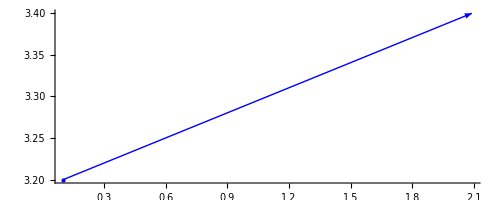

```mathematica
hf//DomainPlot
```

#### addition and mult

```mathematica
(hf+hf2)[x]-(Sech[x]+Exp[-x^2])//Chop
```

0

```mathematica
(hf hf2)[x]-(Sech[x] Exp[-x^2])//Chop
```

0

```mathematica
Sin[hf][x]-Sin[Sech[x]]//Chop
```

0

#### Values Derivatives and Integrals

```mathematica
hf[x]-Sech[x]//Chop
```

0

```mathematica
hf'[x]-Sech'[x]//Chop
```

0

```mathematica
hf''[x]-Sech''[x]//Chop
```

0

```mathematica
(hf//ReduceDimensionIntegrate//Derivative)-hf//Chop//Values//Norm
```

0

```mathematica
Integrate[hf][x]-NIntegrate[Sech[MapFromInterval[hf,z]] MapFromIntervalD[hf,z],{z,-1,MapToInterval[hf,x]}]//Chop
```

0

## Vector Interval

### Random Ray

```mathematica
d=Interval[{.1+3.2 I,-.2-.1 I}];
f={Cos[#],AiryAi[#]}&;
n=300;hf=IFun[f,d,n];
f2={Exp[-#^2],BesselJ[0,#]}&;
hf2=IFun[f2,d,n];
x=MapFromInterval[hf,0.1];
```

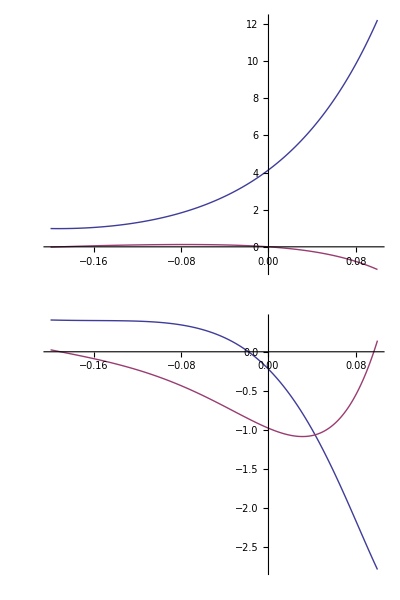
(-Graphics-)

```mathematica
hf
```

```mathematica
hf//DomainPlot
```

-Graphics-

#### addition and mult

```mathematica
(hf+hf2)[x]-(f[x]+f2[x])//Chop
```

{0,0}

```mathematica
(hf hf2)[x]-(f[x] f2[x])//Chop
```

{0,0}

```mathematica
Sin[hf][x]-Sin[f[x]]//Chop
```

{0,0}

#### Values Derivatives and Integrals

```mathematica
hf[x]-f[x]//Chop
```

{0,0}

{0,0}

```mathematica
(Derivative[1]/@(hf//ToArrayOfFuns)//ToArrayFun)[x]-f'[x]//Chop
```

{0,0}

{0,0}

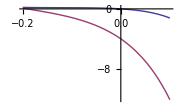
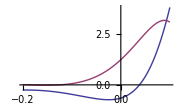

```mathematica
ArrayMap[Derivative[1],hf//ToArrayOfFuns]
```

```mathematica
hf'[x]-f'[x]//Chop
```

{0,0}

```mathematica
(hf')'[x]-hf''[x]
```

{0.+0. ⅈ,0.+0. ⅈ}

```mathematica
hf''[x]-f''[x]//Chop
```

{0,0}

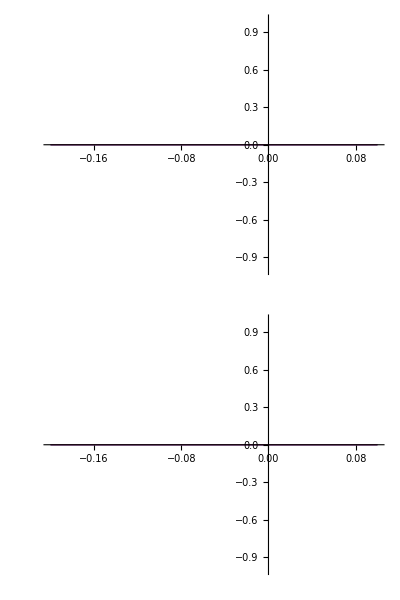
(-Graphics-)

```mathematica
(hf//Integrate)-ToArrayFun[Integrate/@(hf//ToArrayOfFuns)]//Chop
```

```mathematica
(hf//ReduceDimensionIntegrate//Derivative)-hf//Chop//Values//Norm
```

1.29578×10^-10

```mathematica
Integrate[hf][x]-NIntegrate[f[MapFromInterval[hf,z]] MapFromIntervalD[hf,z],{z,-1,MapToInterval[hf,x]}]//Chop
```

{0,0}

```mathematica
d
```

## Matrix Interval

### Random Ray

```mathematica
d=Interval[{.1+3.2 I,-.2-.1 I}];
f=({{Cos[#], AiryAi[#]}, {Exp[#], AiryBi[#]}})&;
n=300;hf=IFun[f,d,n];
f2=({{Exp[-#^2], BesselJ[0,#]}, {Cos[#], Sin[#]}})&;
hf2=IFun[f2,d,n];
x=MapFromInterval[hf,0.1];
```

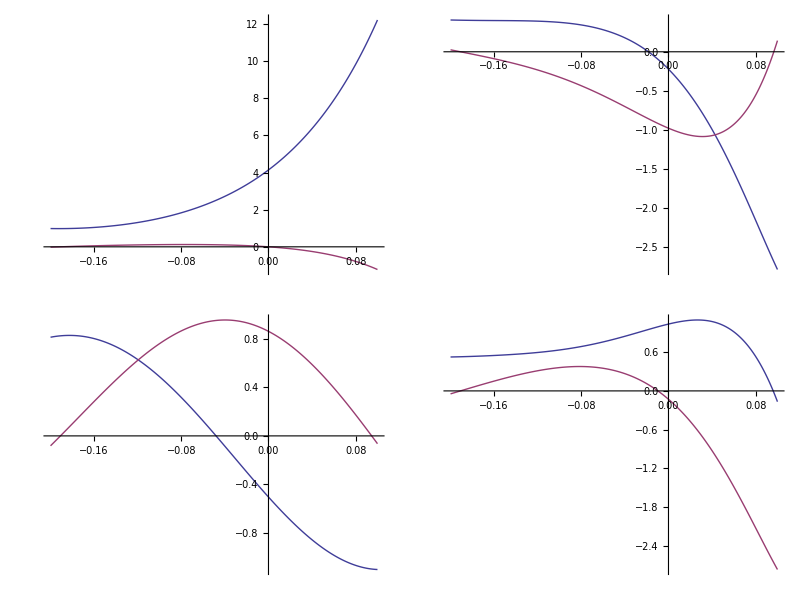
(-Graphics-)

```mathematica
hf
```

```mathematica
hf//DomainPlot
```

-Graphics-

#### addition and mult

```mathematica
(hf+hf2)[x]-(f[x]+f2[x])//Chop//Norm
```

0

```mathematica
(hf hf2)[x]-(f[x] f2[x])//Chop//Norm
```

0

```mathematica
Sin[hf][x]-Sin[f[x]]//Chop//Norm
```

0

#### Values Derivatives and Integrals

```mathematica
hf[x]-f[x]//Chop//Norm
```

0

```mathematica
(MatrixMap[Derivative[1],(hf//ToArrayOfFuns)]//ToArrayFun)[x]-f'[x]//Chop//Norm
```

0

```mathematica
hf'[x]-f'[x]//Chop//Norm
```

0

```mathematica
(hf')'[x]-hf''[x]//Norm
```

0.

```mathematica
hf''[x]-f''[x]//Chop//Norm
```

0

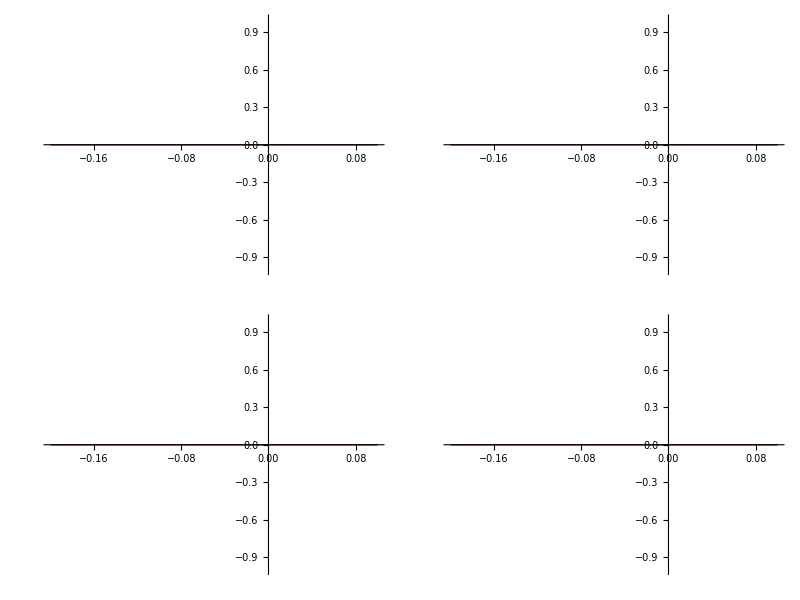
(-Graphics-)

```mathematica
(hf//Integrate)-ToArrayFun[MatrixMap[Integrate,(hf//ToArrayOfFuns)]]//Chop
```

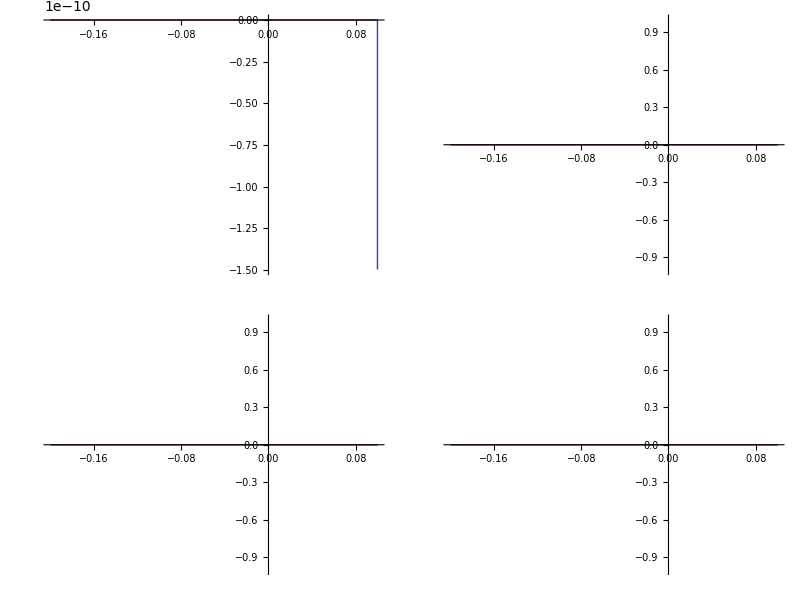
(-Graphics-)

```mathematica
(hf//ReduceDimensionIntegrate//Derivative)-hf//Chop
```

```mathematica
Integrate[hf][x]-NIntegrate[f[MapFromInterval[hf,z]] MapFromIntervalD[hf,z],{z,-1,MapToInterval[hf,x]}]//Chop
```

{{0,0},{0,0}}

## LFun Unit Circle

```mathematica
f=Exp;
lf=LFun[f,Circle[0,1.],200];
f2=Sech[#]Sin[1/#]&;
lf2=LFun[f2,Circle[0,1.],200];
x=Exp[I 0.1];
```

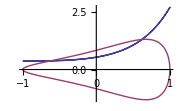

```mathematica
lf
```

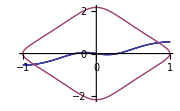

```mathematica
lf2
```

```mathematica
lf[x]-f[x]//Chop
```

0

```mathematica
(lf+lf2)[x]-(f[x]+f2[x])//Chop
```

0

```mathematica
(lf lf2)[x]-(f[x]f2[x])//Chop
```

0

```mathematica
lf2'[x]-f2'[x]//Chop
```

0

```mathematica
lf2''[x]-f2''[x]//Chop
```

0

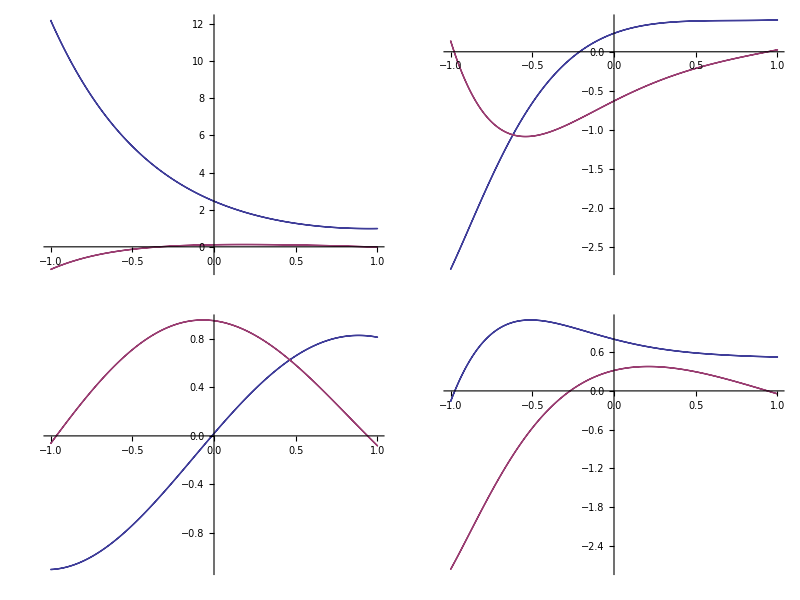
(-Graphics-)

```mathematica
hf//LFun
```

## Real Line

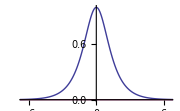

```mathematica
f=Sech;
rf=LFun[f,RealLine,400]
```

```mathematica
rf[0.3]-f[0.3]//Chop
```

0

```mathematica
rf'[0.3]-f'[0.3]//Chop
```

0

## Playground

```mathematica
1
```

1

```mathematica
IFun[Exp/@NChebyshevLobattoPoints[20,0,1],Interval[{0,1}]][0.1]
```

1.10517

{0.,0.0301537,0.116978,0.25,0.413176,0.586824,0.75,0.883022,0.969846,1.}

```mathematica
IFun[Exp[Points[Interval[{0,1}],10]],Interval[{0,1}]][0.1]
```

1.10517

Interval[{0,∞},Stretch→1]

```mathematica
MapFromInterval[Interval[{0,∞},Stretch->1],{-1.,1.}]
```

Power::infy: Infinite expression 1/0.` encountered.

{0.,ComplexInfinity}

```mathematica
?ReImLinePlot
```

Common`ReImLinePlot

ReImLinePlot[Private`sl_ShiftList,Private`opts___]:=Private`ReImListLinePlot[Thread[{Indices[Private`sl],ToList[Private`sl]}],Private`opts]

IFun[{1.,1.,0.999999,0.999997,0.999992,0.99998,0.999958,0.999923,0.999867,0.999786,0.999672,0.999517,0.99931,0.999042,0.9987,0.998271,0.997738,0.997086,0.996295,0.995344,0.99421,0.992868,0.991289,0.989442,0.987293,0.984803,0.981934,0.978638,0.974869,0.970573,0.965692,0.960165,0.953926,0.946905,0.939027,0.930212,0.920379,0.909441,0.897313,0.883904,0.869128,0.8529,0.835138,0.815771,0.794735,0.771982,0.74748,0.72122,0.693218,0.663518,0.632198,0.599373,0.565194,0.529852,0.493576,0.45663,0.419312,0.381947,0.344878,0.30846,0.273049,0.238994,0.206622,0.176234,0.14809,0.122402,0.0993279,0.0789641,0.0613417,0.0464238,0.0341067,0.0242221,0.0165448,0.0108033,0.00669451,0.00390203,0.0021162,0.00105366,0.000473686,0.000188296,0.0000644484,0.0000183559,4.16117×10^-6,7.07933×10^-7,8.35183×10^-8,6.13162×10^-9,2.40775×10^-10,4.07028×10^-12,2.15093×10^-14,2.18173×10^-17,1.96067×10^-21,4.3188×10^-27,2.42117×10^-35,4.68574×10^-48,3.85719×10^-69,5.90917×10^-108,8.17372×10^-192,2.06473296863×10^-431,3.075289257×10^-1725,0},Interval[{0,∞},Stretch→1]]

```mathematica
FinitePoints[hf//Domain,hf//Length]
```

{0.,0.000251792,0.00100768,0.00226918,0.00403884,0.00632025,0.00911804,0.0124379,0.0162867,0.0206722,0.0256036,0.0310912,0.0371465,0.0437823,0.0510127,0.0588535,0.0673216,0.0764359,0.0862165,0.0966857,0.107867,0.119788,0.132474,0.145958,0.160272,0.175451,0.191533,0.208561,0.226578,0.245633,0.265777,0.287067,0.309564,0.333333,0.358445,0.384978,0.413013,0.442642,0.473963,0.507082,0.542115,0.579188,0.618439,0.660017,0.704088,0.750831,0.800442,0.853139,0.909159,0.968764,1.03224,1.09992,1.17214,1.24931,1.33186,1.42028,1.51511,1.61698,1.72656,1.84463,1.97207,2.10987,2.25916,2.42123,2.59755,2.78982,3.,3.23035,3.4835,3.76255,4.07112,4.41349,4.79476,5.22102,5.6996,6.2394,6.85128,7.54863,8.34811,9.27064,10.3428,11.5987,13.0829,14.8541,16.9913,19.603,22.8403,26.9205,32.1634,39.057,48.3742,61.4,80.3994,109.673,158.222,247.596,440.689,992.382,3971.53}

```mathematica
hf//Values
```

{1.,1.,0.999999,0.999997,0.999992,0.99998,0.999958,0.999923,0.999867,0.999786,0.999672,0.999517,0.99931,0.999042,0.9987,0.998271,0.997738,0.997086,0.996295,0.995344,0.99421,0.992868,0.991289,0.989442,0.987293,0.984803,0.981934,0.978638,0.974869,0.970573,0.965692,0.960165,0.953926,0.946905,0.939027,0.930212,0.920379,0.909441,0.897313,0.883904,0.869128,0.8529,0.835138,0.815771,0.794735,0.771982,0.74748,0.72122,0.693218,0.663518,0.632198,0.599373,0.565194,0.529852,0.493576,0.45663,0.419312,0.381947,0.344878,0.30846,0.273049,0.238994,0.206622,0.176234,0.14809,0.122402,0.0993279,0.0789641,0.0613417,0.0464238,0.0341067,0.0242221,0.0165448,0.0108033,0.00669451,0.00390203,0.0021162,0.00105366,0.000473686,0.000188296,0.0000644484,0.0000183559,4.16117×10^-6,7.07933×10^-7,8.35183×10^-8,6.13162×10^-9,2.40775×10^-10,4.07028×10^-12,2.15093×10^-14,2.18173×10^-17,1.96067×10^-21,4.3188×10^-27,2.42117×10^-35,4.68574×10^-48,3.85719×10^-69,5.90917×10^-108,8.17372×10^-192,2.06473296863×10^-431,3.075289257×10^-1725,0}

```mathematica
hf2=IFun[0.5Exp[-#]&,hf//Domain,hf//Length];
```

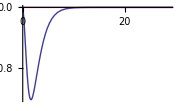

```mathematica
IFun[ChebyshevLobattoDerivative[Values[hf]],hf//Domain]
```

```mathematica
?IFun
```

Global`IFun

```mathematica
?MapToIntervalD
```

Common`MapToIntervalD

MapToIntervalD[Interval[{Private`a_,Private`b_}],Private`x_]:=-2/(Private`a-Private`b)

```mathematica
MapToIntervalD[hf//Domain,#]&/@(IFun[Exp[-#]&,hf//Domain,3]//Points)
```

{2.,0.5,0}

```mathematica
hf'[3.]
```

-0.0988367

```mathematica
3. 0.5 Exp[-3.]
```

0.0746806

```mathematica
Sech'[3.]
```

-0.0988367

```mathematica
hf''[3.]
```

0.097368

```mathematica
Sech''[3.]
```

0.097368

```mathematica
hf//Integrate//Values
```

{4.39626×10^-14,0.000995983,0.00389088,0.00902367,0.0155955,0.0251409,0.0352109,0.049474,0.0629033,0.082219,0.098914,0.12365,0.14357,0.174131,0.197298,0.234136,0.260644,0.304266,0.3343,0.385292,0.419144,0.478191,0.516291,0.584219,0.627171,0.705,0.753639,0.842669,0.898145,1.00008,1.06399,1.18117,1.25576,1.39146,1.48002,1.63912,1.74661,1.93674,2.07113,2.3051,2.48015,2.78158,3.02378,3.44254,3.8114,4.47746,5.14502,6.55728,8.34033,16.0032,56.6681,93.6168,99.4337,100.417,101.095,101.329,101.527,101.61,101.685,101.721,101.75,101.769,101.778,101.79,101.79,101.8,101.795,101.804,101.797,101.806,101.798,101.806,101.799,101.806,101.799,101.806,101.799,101.806,101.8,101.805,101.8,101.805,101.8,101.805,101.801,101.804,101.801,101.804,101.801,101.804,101.802,101.803,101.802,101.803,101.802,101.803,101.802,101.803,101.803,101.803,101.803}

```mathematica
MapFromIntervalD[hf,1.]
```

0.

```mathematica
hf//Integrate//Values//Last
```

1.5708

```mathematica
(MapFromInterval[hf,0.1+0.0000001]-MapFromInterval[hf,0.1])/0.0000001
```

2.46914

```mathematica
MapFromIntervalD[hf,0.1]
```

2.46914

```mathematica
MapToInterval[hf,MapFromInterval[hf,0.1]]
```

0.1

```mathematica
∫_0^∞ Sech[x]ⅆx//N
```

1.5708

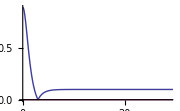

```mathematica
hf-0.1//Abs
```

```mathematica
(hf2+hf)[3.]
```

0.124221

```mathematica
Random[]
```

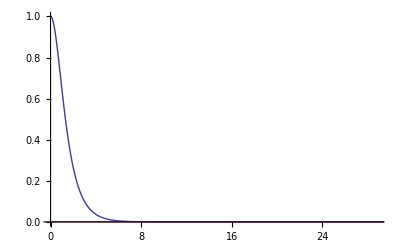

```mathematica
hf//ReImLinePlot
```

```mathematica
hf
```

-Graphics-

```mathematica
hf//FiniteValues
```

{1.,1.,0.999999,0.999997,0.999992,0.99998,0.999958,0.999923,0.999867,0.999786,0.999672,0.999517,0.99931,0.999042,0.9987,0.998271,0.997738,0.997086,0.996295,0.995344,0.99421,0.992868,0.991289,0.989442,0.987293,0.984803,0.981934,0.978638,0.974869,0.970573,0.965692,0.960165,0.953926,0.946905,0.939027,0.930212,0.920379,0.909441,0.897313,0.883904,0.869128,0.8529,0.835138,0.815771,0.794735,0.771982,0.74748,0.72122,0.693218,0.663518,0.632198,0.599373,0.565194,0.529852,0.493576,0.45663,0.419312,0.381947,0.344878,0.30846,0.273049,0.238994,0.206622,0.176234,0.14809,0.122402,0.0993279,0.0789641,0.0613417,0.0464238,0.0341067,0.0242221,0.0165448,0.0108033,0.00669451,0.00390203,0.0021162,0.00105366,0.000473686,0.000188296,0.0000644484,0.0000183559,4.16117×10^-6,7.07933×10^-7,8.35183×10^-8,6.13162×10^-9,2.40775×10^-10,4.07028×10^-12,2.15093×10^-14,2.18173×10^-17,1.96067×10^-21,4.3188×10^-27,2.42117×10^-35,4.68574×10^-48,3.85719×10^-69,5.90917×10^-108,8.17372×10^-192,2.06473296863×10^-431,3.075289257×10^-1725}

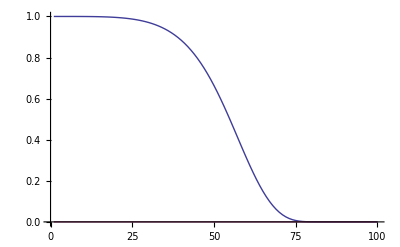

```mathematica
IFun[Sech,Interval[{0,∞},Stretch->1],100]//Values//ReImListLinePlot
```

```mathematica
?ReImLinePlot
```

Common`ReImLinePlot

ReImLinePlot[Private`sl_ShiftList,Private`opts___]:=Private`ReImListLinePlot[Thread[{Indices[Private`sl],ToList[Private`sl]}],Private`opts]

```mathematica
IFun[Sech[Points[Interval[{0,∞},Stretch->1],50]],Interval[{0,∞},Stretch->1]][0.3]
```

0.956628

```mathematica
Sech[0.3]
```

0.956628

```mathematica
Exp[0.1]
```

1.10517

```mathematica
?IFun
```

Global`IFun

IFun[l_List,d_Domain][z_]:=ChebyshevLobattoBarycentricInterpolation[l,MapToInterval[d,z]]

## Arc

```mathematica
f=Sech;
af=IFun[Sech,Arc[0.,1.,{-0.1,0.1}]];
```

```mathematica
af[Exp[I 0.001]]-f[Exp[I 0.001]]//Chop
```

0

```mathematica
af[1.]-f[1.]//Chop
```

0

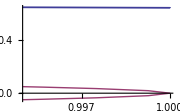

```mathematica
af
```

## ValueList

```mathematica
l={IFun[Sech,Line[{-∞,-1.}]],IFun[Sech,Line[{-1.,1.}]],IFun[Sech,Line[{1.,∞}]]};
```

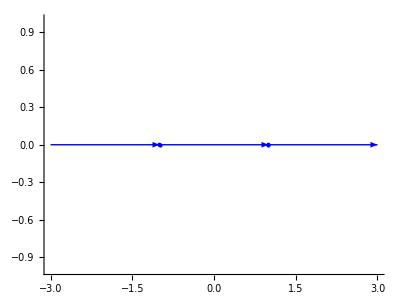

```mathematica
l//DomainPlot
```

```mathematica
(l//ToValueList)-(Flatten[Values/@l]//Rest//Most)//Norm//Chop
```

0

```mathematica
l⟦1⟧//ScalarFunQ
```

True

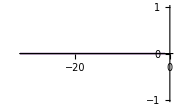

```mathematica
FromValueList[l⟦1⟧,l⟦1⟧//ToValueList]-l⟦1⟧//Chop
```

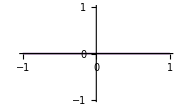
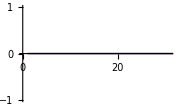
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
FromValueList[l,l//ToValueList]-l
```

```mathematica
fv={Sech[#],Exp[-#^2]}&;
lv={IFun[f,Line[{-∞,-1.}]],IFun[f,Line[{-1.,1.}]],IFun[f,Line[{1.,∞}]]};
```

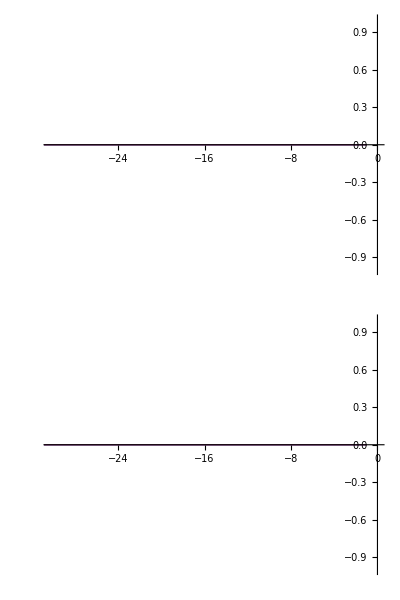
(-Graphics-)

```mathematica
FromValueList[l⟦1⟧,l⟦1⟧//ToValueList]-l⟦1⟧
```

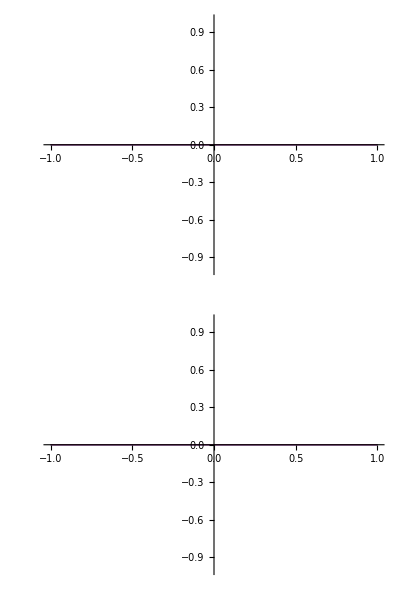
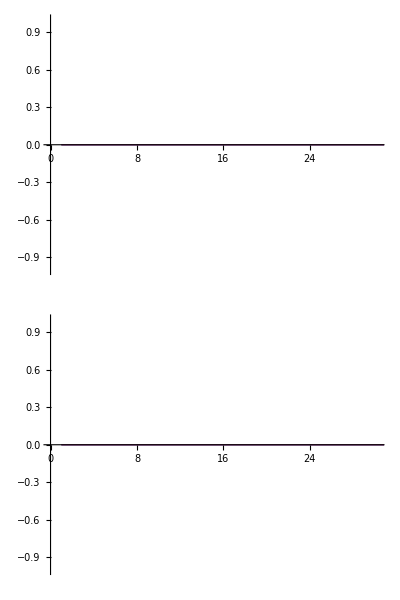
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
FromValueList[l,l//ToValueList]-l
```

```mathematica
f[z_]:=({{Sech[z], Exp[-z^2]}, {z Sech[z], z^2 Exp[-z^2]}});
f[_?InfinityQ]:=({{0, 0}, {0, 0}});
l={IFun[f,Line[{-∞,-1.}]],IFun[f,Line[{-1.,1.}]],IFun[f,Line[{1.,∞}]]};
lV=#⟦All,1⟧&/@l;
```

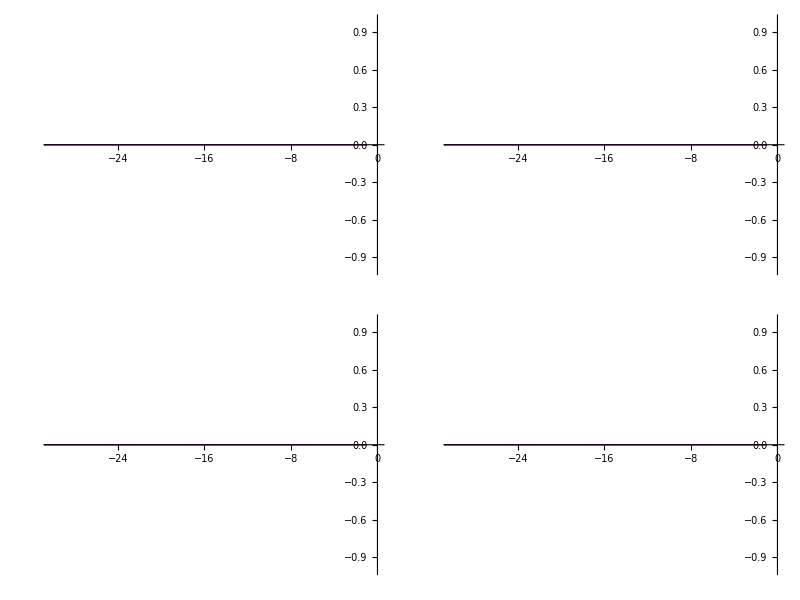
(-Graphics-)

```mathematica
FromValueList[l⟦1⟧,l⟦1⟧//ToValueList]-l⟦1⟧
```

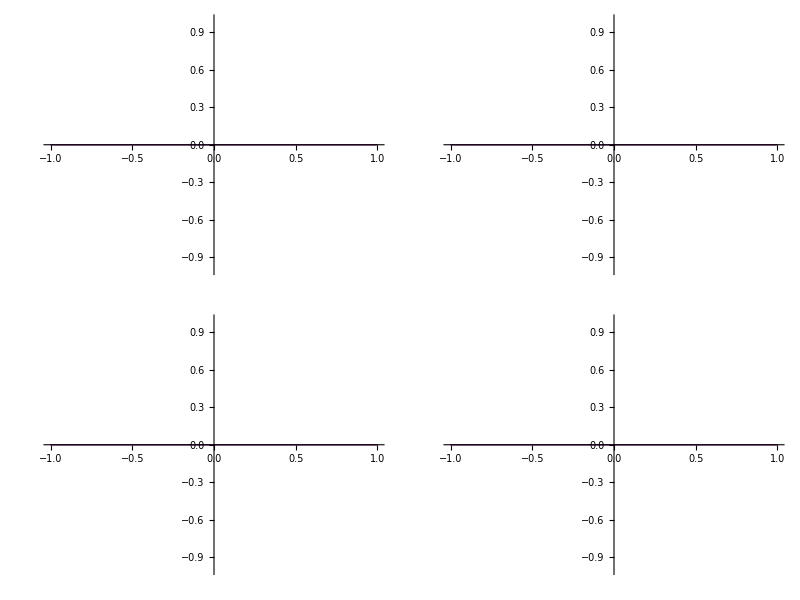
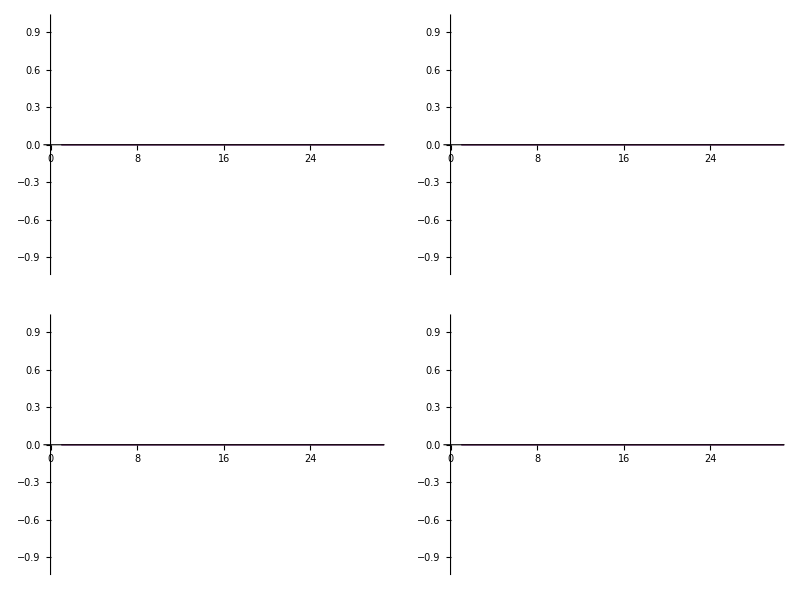
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
FromValueList[l,l//ToValueList]-l
```

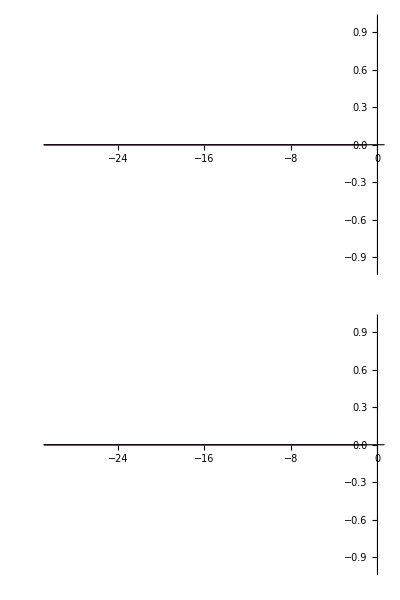
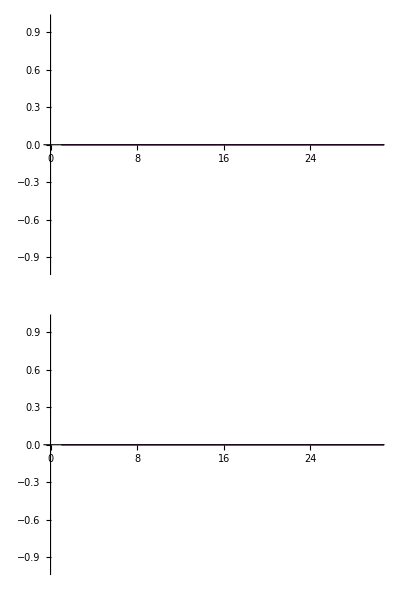
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
FromValueList[lV,MatrixMultVectorFun[l].ToValueList[lV]]-(#⟦1⟧.#⟦2⟧&/@Thread[{l,lV}])
```

```mathematica
FromValueList[l,MatrixMultMatrixFun[l].ToValueList[l]]-(#⟦1⟧.#⟦2⟧&/@Thread[{l,l}])
```

{(-Graphics-),(-Graphics-),(-Graphics-)}